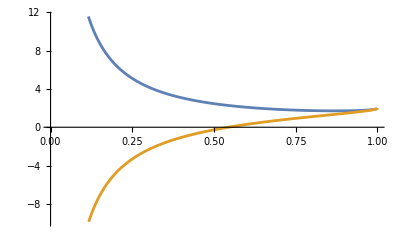

```mathematica
m1 = ToExpression["\\sqrt{2} \\frac{\\sqrt{1+\\mathcal{O}}-\\sqrt{1-\\mathcal{O}} \\mathcal{O}}{\\mathcal{O}}",TeXForm];
m2 = ToExpression["\\sqrt{2} \\frac{\\mathcal{O} \\sqrt{1+\\mathcal{O}}-\\sqrt{1-\\mathcal{O}}}{\\mathcal{O}}",TeXForm];


Plot[{m1,m2},{O,0,1}]
```

```mathematica
expr1 = 1/2 (1-O^2)p^2+ 1/2 O *((w1^2+m1 p w1) - (w2^2-m2 p w2));
expr2 = O/2*((w1+m1 p/2)^2 -(w2-m2 p/2)^2);
expr1 - expr2 //FullSimplify
```

0

```mathematica
$Assumptions = {O>-1,p>0}
```

{O>-1,p>0}

```mathematica
expr1
```

-((-1+O^2) p)/(2 √(1+O^2-2 O √(1-O^2)))

```mathematica
O/2 √(m1^2+m2^2)//FullSimplify
```

√(1+O^2-2 O √(1-O^2))

```mathematica
expr1=(1/2(1-O^2)p^2 )/√((O/2 √(m1^2+m2^2) p)^2)//Simplify;
expr2 = ToExpression["\\frac{\\left(1-\\mathcal{O}^2\\right) \\rho^2}{2 \\sqrt{\\mathcal{O}^2-4 \\sqrt{1-\\mathcal{O}^2} \\mathcal{O} \\rho^2+2\\left(\\mathcal{O}^2+1\\right) \\rho^2}}",TeXForm]/.ρ-> p;
expr1 - expr2//FullSimplify
```

1/2 (-1+O^2) p (-1/(√(1+O^2-2 O √(1-O^2)))+p/(√(O^2-4 O √(1-O^2) p^2+2 (1+O^2) p^2)))

The original zscore I derived does not agree with what I computed. There is a term in denominator which makes it grow as p^2 instead of just p. I also am off by a factor of sqrt(2)

```mathematica
expr1/p/.p->0/.O-> 0.5
expr2/p*√2/.p->0/.O-> 0.5
```

0.605174

0

```mathematica
O^2-4 O √(1-O^2) p^2+2 (1+O^2)//Simplify
```

2+3 O^2-4 O √(1-O^2) p^2

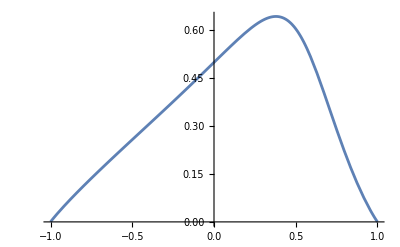

```mathematica
Plot[{expr1/p },{O,-1,1}]
```

```mathematica
expr1/p//FullSimplify
```

-(-1+O^2)/(2 √(1+O^2-2 O √(1-O^2)))

```mathematica
1+O^2-2 O √(1-O^2)//FullSimplify
```

1+O^2-2 O √(1-O^2)

```mathematica
Series[expr1 /.O -> 1-ϵ, {ϵ,0,1}]
%/.ϵ-> 1-O
```

(p ϵ)/(√2)+1/2 p ϵ^(3/2)+O[ϵ]^2

SeriesData::sdatv: First argument 1-O is not a valid variable.

(p (1-O))/(√2)+1/2 p (1-O)^(3/2)+O[1-O]^2